{{ψ1→InterpolatingFunction[{{0., 15.}, {…, -60., 60., …}}, <>],ψ2→InterpolatingFunction[{{0., 15.}, {…, -60., 60., …}}, <>]}}

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

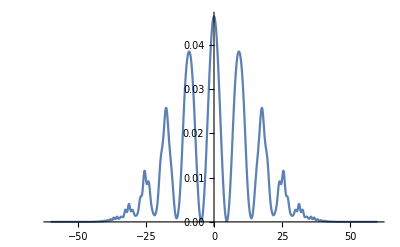

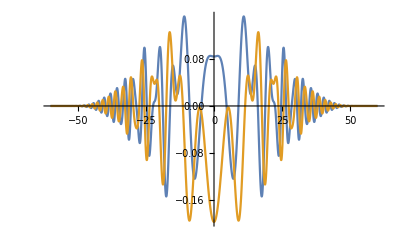

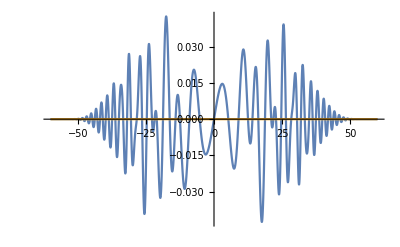

```mathematica
ћ=1;
m=1;
c=4;
z=5;
ψ10=(ⅇ^(z^2) (ⅇ^(-(-z+x)^2)+ⅇ^(-(z+x)^2)))/(√(1+ⅇ^(2 z^2)) (2 π)^(1/4));

ψ20=0;
time=15;

s=NDSolve[{I*ћ*D[ψ1[t,x],t]==-I*ћ*c*D[ψ2[t,x],x]+m*c^2*ψ1[t,x],I*ћ*D[ψ2[t,x],t]==-I*ћ*c*D[ψ1[t,x],x]-m*c^2*ψ2[t,x],ψ1[t,-60]==ψ1[t,60],ψ1[0,x]==ψ10,ψ2[t,-60]==ψ2[t,60],ψ2[0,x]==ψ20},{ψ1,ψ2},{t,0,time},{x,-60,60}]

DensityPlot[(Abs[ψ1[t,x]]^2+Abs[ψ2[t,x]]^2)/.%,{t,0,time},{x,-60,60},PlotPoints->250]
DensityPlot[Abs[Re[ψ1[t,x]]]/.s,{t,0,time},{x,-60,60},PlotPoints->250]
DensityPlot[Abs[Im[ψ1[t,x]]]/.s,{t,0,time},{x,-60,60},PlotPoints->250]
DensityPlot[Abs[Re[ψ2[t,x]]]/.s,{t,0,time},{x,-60,60},PlotPoints->250]
DensityPlot[Abs[Im[ψ2[t,x]]]/.s,{t,0,time},{x,-60,60},PlotPoints->250]
Plot[(Abs[ψ1[time,x]]^2+Abs[ψ2[time,x]]^2)/.s,{x,-60,60},PlotPoints->250,PlotRange->Full]
Plot[{Re[ψ1[time,x]]/.s,Im[ψ1[time,x]]/.s},{x,-60,60},PlotPoints->250,PlotRange->Full]
Plot[{Re[ψ2[time,x]]/.s,Im[ψ2[time,x]]/.s},{x,-60,60},PlotPoints->250,PlotRange->Full]
```